# Eli — EIWL Sections 35, 36

```mathematica
(*35.1*)Interpreter["Location"]["eiffel tower"]
```

GeoPosition[{48.8583,2.29444}]

```mathematica
(*35.2*)Interpreter["University"]["U of T"]
```

University of Toronto

```mathematica
(*35.3*)Interpreter["Chemical"][{"C2H4","C2H6","C3H8"}]
```

{ethylene,ethane,propane}

```mathematica
(*35.4*)Interpreter["Date"]["20140108"]
```

Wed 8 Jan 2014

```mathematica
(*35.5*)Interpreter["University"][Table[StringJoin["U of ",Capitalize[FromLetterNumber[x]]],{x,26}]]
```

{Failure[…],University of Birjand,University of California-Berkeley,Failure[…],The University of Edinburgh,Failure[…],University of Georgia,University of Houston,University of Illinois at Urbana-Champaign,Failure[…],Failure[…],University of Lethbridge,University of Michigan-Ann Arbor,Failure[…],Failure[…],University of Phoenix-Online Campus,Failure[…],University of Regina,University of Saskatchewan,University of Toronto,Failure[…],Failure[…],Failure[…],Failure[…],Failure[…],Failure[…]}

```mathematica
(*35.6*)Interpreter["Movie"][CommonName[EntityList[]]]
```

{Failure[…],Failure[…],Phoenix,Failure[…],Failure[…],Failure[…],Failure[…],Failure[…],Failure[…],Failure[…],Honolulu,Failure[…],Failure[…],Failure[…],Failure[…],Topeka,Failure[…],Failure[…],Failure[…],Annapolis,Failure[…],Failure[…],Failure[…],Failure[…],Failure[…],Failure[…],Lincoln,Failure[…],Failure[…],Failure[…],Santa Fe,Failure[…],Failure[…],Expedition: Bismarck,Columbus,Failure[…],Failure[…],Failure[…],Providence,Failure[…],Failure[…],Nashville,Failure[…],Failure[…],Failure[…],Failure[…],Olympia,Failure[…],Madison,Cheyenne}

```mathematica
(*35.7*)Interpreter["City"][StringJoin[#]&/@Permutations[{"a","i","l","m"}]]
```

{Failure[…],Failure[…],Alim,Failure[…],Failure[…],Amli,Balm,Failure[…],Ilam,Failure[…],Failure[…],Failure[…],Failure[…],Lami,Failure[…],Lima,Lamai,Failure[…],Failure[…],Mali,Failure[…],Milah,Mali,Failure[…]}

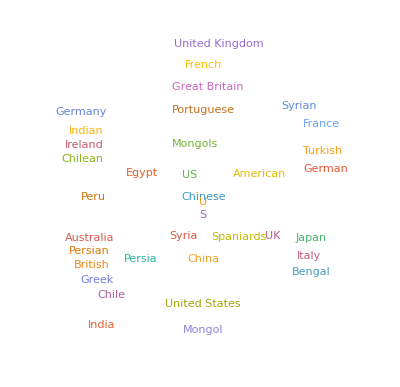

```mathematica
(*35.8*)WordCloud[TextCases[WikipediaData["gunpowder"],"Country"]]
```

```mathematica
(*35.9*)TextCases["She sells sea shells by the sea shore","Noun"]
```

{sea,shells,sea,shore}

```mathematica
(*35.10*)Length[#]&/@Values[TextCases[StringJoin[Characters[WikipediaData["Computers"]][[1;;1000]]],{"Noun","Verb","Adjective"}]]
```

{54,23,20}

```mathematica
(*35.11*)TextStructure[TextSentences[WikipediaData["computers"]][[1]]]
```

A
Determinercomputer
Noun
Noun Phrase  is
Verb    a
Determinermachine
Noun
Noun Phrase    that
Wh-Determiner
Wh-Noun Phrase  can
Verb  be
Verb  programmed
Verb    to
Preposition    automatically
Adverb
Adverb Phrasecarry
Verb  out
Particle
Particle    sequences
Noun
Noun Phrase  of
Preposition      arithmetic
Adjectiveor
Conjunctionlogical
Adjective
Adjective Phraseoperations
Noun
Noun Phrase  (
Punctuation  computation
Noun
Noun Phrase)
Punctuation
Parenthetical
Noun Phrase
Prepositional Phrase
Noun Phrase
Verb Phrase
Verb Phrase
Clause
Verb Phrase
Verb Phrase
Verb Phrase
Clause
Noun Phrase
Verb Phrase.
Punctuation
Sentence

```mathematica
(*35.12*)Keys[Reverse[Sort[Counts[TextCases[ExampleData[{"Text","AliceInWonderland"}],"Noun"]]]][[1;;10]]]
```

{Rabbit,door,voice,time,Mouse,way,moment,thing,head,garden}

```mathematica
(*35.13*)words:=TextWords[TextSentences[WikipediaData["language"]][[1]]];
words
```

{Language,is,a,structured,system,of,communication,that,consists,of,grammar,and,vocabulary}

```mathematica
CommunityGraphPlot[words[[#]]->words[[#+1]]&/@Range[Length[words]-1]]
```

-Graphics-

```mathematica
(*35.14*)Length[#]&/@Values[TextCases[StringJoin[Riffle[WordList[][[1;;50]],Table[" ",Length[WordList[][[1;;50]]]]]],{"Noun","Verb","Adjective","Adverb"}]] (*My computer hates the whole wordlist*)
```

{29,9,8,2}

```mathematica
(*35.15*)Flatten[WordTranslation[IntegerName[Range[9]+1],"French"]]
```

{deux,trois,quatre,cinq,six,sept,huit,neuf,dix}

```mathematica
(*36.1*)CloudPublish[Style[RandomInteger[1000],FontSize->100]]
```

CloudObject[https://www.wolframcloud.com/obj/03b6bac7-ecbe-464e-8358-b603c431e055]

```mathematica
(*36.2*)CloudPublish[FormFunction[{"x"->"Number"},#x^#x&]]
```

CloudObject[https://www.wolframcloud.com/obj/ca260cc3-3f4d-42a6-9f9b-2701647210b1]

```mathematica
(*36.3*)CloudPublish[FormFunction[{"x" -> "Number", "y" -> "Number"}, #x^#y &]]
```

CloudObject[https://www.wolframcloud.com/obj/0047c168-4a9e-4794-b09e-700bdd0d57f8]

```mathematica
(*36.4*)CloudPublish[FormFunction[{"page"->"String"},WordCloud[WikipediaData[#page]]&]]
```

CloudObject[https://www.wolframcloud.com/obj/04f9f46f-26c0-4d5e-9f65-0b1423bbdcc2]

```mathematica
(*36.5*)CloudPublish[FormFunction[{"string"->"String"},Style[StringReverse[#string],50]&]]
```

CloudObject[https://www.wolframcloud.com/obj/80882c6c-d67e-4245-acf5-76ffce4b8594]

```mathematica
(*36.6*)CloudPublish[FormFunction[{"n"->"Integer"},Graphics[Style[RegularPolygon[#n],RandomColor[]]]&]]
```

CloudObject[https://www.wolframcloud.com/obj/a3537411-5ad6-4412-b3c8-97409efd1567]

```mathematica
(*36.7*)
```

```mathematica
CloudPublish[FormFunction[{"location"->"String","n"->"Integer"},GeoNearest["Volcano",GeoPosition[Interpreter["Location"][#location]]&,#n&]]]
```

GeoNearest::invloc: GeoPosition[Interpreter[Location][#location]]& is not a valid location specification.

CloudObject[https://www.wolframcloud.com/obj/aa01551a-52a8-4dd8-9e19-d8cbd818ea17]